## Random walk distribution function

```mathematica
Pw[n_,p_,k_]:=1/(√(2 π)√(4 n p (1-p)))Exp[-1/2(k-n(p-(1-p)))^2/(4 n p (1-p))]
```

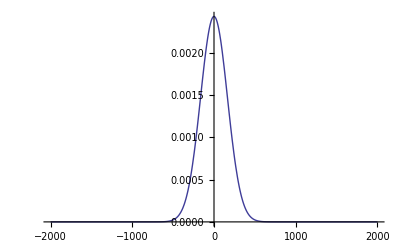

```mathematica
Plot[ Pw[ 30^3,0.5,k],{k,-2000,2000},PlotRange->All]
```

```mathematica
NIntegrate[ k^2/30^3 Pw[30^3,0.5,k],{k,-2000,2000}]
```

1.

## Distribution function for S(Q) = X^2/n

```mathematica
Pf[n_,p_,s_]:= 1/2(√(n/s))/(√(2π)√(4 n p(1-p)))(Exp[-1/2(√(s n)- n(p-(1-p)))^2/(4 n p(1-p))]+Exp[-1/2(-√(s n)- n(p-(1-p)))^2/(4 n p(1-p))])
```

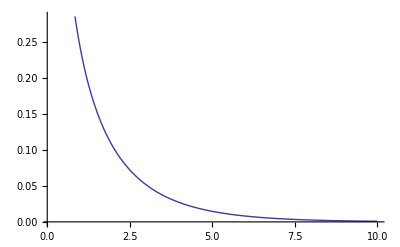

```mathematica
Plot[ Pf[ 20^3,0.5, s],{s,0.1,10}]
```

```mathematica
Norma[n_,p_]:=Module[{xlim},
xlim=10.(n(p-(1-p)))^2/n+200.;
NIntegrate[  Pf[n,p,s],{s,0.0,xlim}]]
Mu[n_,p_]:=Module[{xlim},
xlim=10.(n(p-(1-p)))^2/n+200.;
NIntegrate[ s Pf[n,p,s],{s,0.0,xlim}]]
Var[n_,p_]:=Module[{xlim},
xlim=10.(n(p-(1-p)))^2/n+200.;
NIntegrate[ s^2 Pf[n,p,s],{s,0.0,xlim}]-NIntegrate[ s Pf[n,p,s],{s,0,xlim}]^2]
```

```mathematica
Np=20;
pval=0.534;
Norma[Np^3,pval]
Mu[Np^3,pval]
√Var[Np^3,pval]
```

1.

37.9874

12.2174

```mathematica
Np=20;
pval=0.50001;
Norma[Np^3,pval]
Mu[Np^3,pval]
√Var[Np^3,pval]
```

1.

1.

1.41422

### Computing the moments of P(SQ)

```mathematica
s0=Assuming[p>1/2 && p<1 && n>0,Integrate[Pf[n,p,s],{s,0,∞}]]
```

1

```mathematica
s1=Assuming[p>1/2 && p<1 && n>0,Integrate[s Pf[n,p,s],{s,0,∞}]]
```

n (1-2 p)^2-4 (-1+p) p

```mathematica
s2=Assuming[p>1/2 && p<1 && n>0,Integrate[s^2 Pf[n,p,s],{s,0,∞}]]
```

n^2 (1-2 p)^4-24 n (1-2 p)^2 (-1+p) p+48 (-1+p)^2 p^2

### Computing the variance of SQ

```mathematica
FullSimplify[s2-s1^2]
```

-16 (-1+p) p (n (1-2 p)^2-2 (-1+p) p)

```mathematica
Ssig[n_,p_]:=√(-16 (-1+p) p (n (1-2 p)^2-2 (-1+p) p))
```

```mathematica
Ssig[20^3,0.534]
```

12.2174

```mathematica
s1/.{n->20^3,p->0.50001}
```

0.501429

```mathematica
s0=Assuming[p>1/2 && p<1 && n>0,Integrate[ Pf[n,p,s],{s,0,∞}]]
```

1/2 Erfc[(n-2 n p)/(2 √2 √(-n (-1+p) p))]

```mathematica
s0/.{n->20^3,p->0.50001}
```

0.500714

```mathematica
MU = Table[ Mu[N^3,pVal],{pVal,{0.5000001, 0.501, 0.502, 0.504,0.508,0.516,0.54,0.58}},{N,{5,10,20,25,30,40}}]
```

Append::normal: Nonatomic expression expected at position 1 in Append[NIntegrate`StrategiesDump`prepOption, Method → "GlobalAdaptive"].

Append::argrx: Append called with 3 arguments; 2 arguments are expected.

NIntegrate::nsr: Append[NIntegrate`SymbolicPreprocessing, NIntegrate`StrategiesDump`prepOption, Method → "GlobalAdaptive"] is not a valid specification of an integration strategy or rule.

Append::normal: Nonatomic expression expected at position 1 in Append[NIntegrate`StrategiesDump`prepOption, Method → "GlobalAdaptive"].

Append::argrx: Append called with 3 arguments; 2 arguments are expected.

NIntegrate::nsr: Append[NIntegrate`SymbolicPreprocessing, NIntegrate`StrategiesDump`prepOption, Method → "GlobalAdaptive"] is not a valid specification of an integration strategy or rule.

Append::normal: Nonatomic expression expected at position 1 in Append[NIntegrate`StrategiesDump`prepOption, Method → "GlobalAdaptive"].

General::stop: Further output of Append :: normal will be suppressed during this calculation.

Append::argrx: Append called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Append :: argrx will be suppressed during this calculation.

NIntegrate::nsr: Append[NIntegrate`SymbolicPreprocessing, NIntegrate`StrategiesDump`prepOption, Method → "GlobalAdaptive"] is not a valid specification of an integration strategy or rule.

General::stop: Further output of NIntegrate :: nsr will be suppressed during this calculation.

{{0.499869,0.499872,0.499882,0.499887,0.499894,0.499908},{0.517958,0.552361,0.659355,0.732659,0.820775,1.04859},{0.536553,0.609053,0.855373,1.04023,1.27727,1.95053},{0.575293,0.735828,1.37428,1.92452,2.69157,5.09054},{0.659212,1.04841,3.02049,4.99396,7.91097,17.3837},{0.854728,1.94968,9.19064,16.999,28.647,66.535},{1.69989,7.39254,52.1936,100.994,173.794,410.594},{4.16473,26.5744,205.774,400.974,692.174,1639.37}}

```mathematica
SIG= Table[ √Var[N^3,pVal],{pVal,{0.5000001, 0.501, 0.502, 0.504,0.508,0.516,0.54,0.58}},{N,{5,10,20,25,30,40}}]
```

Append::normal: Nonatomic expression expected at position 1 in Append[NIntegrate`StrategiesDump`prepOption, Method → "GlobalAdaptive"].

Append::argrx: Append called with 3 arguments; 2 arguments are expected.

NIntegrate::nsr: Append[NIntegrate`SymbolicPreprocessing, NIntegrate`StrategiesDump`prepOption, Method → "GlobalAdaptive"] is not a valid specification of an integration strategy or rule.

Append::normal: Nonatomic expression expected at position 1 in Append[NIntegrate`StrategiesDump`prepOption, Method → "GlobalAdaptive"].

Append::argrx: Append called with 3 arguments; 2 arguments are expected.

NIntegrate::nsr: Append[NIntegrate`SymbolicPreprocessing, NIntegrate`StrategiesDump`prepOption, Method → "GlobalAdaptive"] is not a valid specification of an integration strategy or rule.

Append::normal: Nonatomic expression expected at position 1 in Append[NIntegrate`StrategiesDump`prepOption, Method → "GlobalAdaptive"].

General::stop: Further output of Append :: normal will be suppressed during this calculation.

Append::argrx: Append called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Append :: argrx will be suppressed during this calculation.

NIntegrate::nsr: Append[NIntegrate`SymbolicPreprocessing, NIntegrate`StrategiesDump`prepOption, Method → "GlobalAdaptive"] is not a valid specification of an integration strategy or rule.

General::stop: Further output of NIntegrate :: nsr will be suppressed during this calculation.

{{3.75562×10^-14,5.05294×10^-13,6.79837×10^-12,1.5697×10^-11,3.10989×10^-11,9.14665×10^-11},{0.000372476,0.00492591,0.0622555,0.137059,0.25583,0.64403},{0.00208801,0.0269934,0.308948,0.628743,1.06654,2.12787},{0.0115713,0.140883,1.2412,2.09398,2.89648,4.29216},{0.0622586,0.644032,3.14931,4.2468,5.44531,8.21695},{0.30898,2.12717,5.89375,8.11976,10.6054,16.2441},{1.78203,5.2369,14.334,19.9854,26.2441,40.3719},{3.79463,10.0835,28.2865,39.5087,51.9222,79.9228}}

```mathematica
S1/VAR
```

{{0.707108,0.70711,0.707117,0.707121,0.707125,0.707135},{0.719836,0.743717,0.815889,0.864091,0.921307,1.06886},{0.732798,0.782297,0.94367,1.06341,1.22175,1.76161},{0.759449,0.866188,1.28956,1.73666,2.83129,2.63187},{0.815903,1.06892,3.91446,2.68988,1.94956,1.60481},{0.943811,1.7627,1.84308,1.60972,1.52238,1.45834},{1.54673,2.00368,1.47077,1.44274,1.43062,1.4211},{3.45566,1.52853,1.42777,1.42113,1.41821,1.4159}}

```mathematica
VAR = Table[ Evaluate[√Re[var]/.{n->N^3, p->pVal}],{pVal,{0.5000001, 0.501, 0.502, 0.504}},{N,{5,10,20,25,30,40}}]
```

{{1.41422,1.41422,1.41423,1.41424,1.41425,1.41427},{1.43947,1.48577,1.61661,1.69609,1.78204,1.9623},{1.46476,1.55743,1.81314,1.95664,2.09107,2.21458},{1.51538,1.6993,2.13155,2.21644,1.90135,0.+3.86841 ⅈ}}

```mathematica
Table[ i, {i,{0,1,2,3}},{j,{5,6,7}}]
```

{{0,0,0},{1,1,1},{2,2,2},{3,3,3}}

```mathematica
√Re[var]/.{n->40^3, p->0.500001}
```

1.11858

```mathematica
√800.
```

28.2843